```mathematica
(*
 * Gourav Siddhad
* Btech Computer Sc. 2nd Yr
* 3235
 *)
NewtonRaphson[xo_,n_,f_]:=
Module[{},xk1;xk=N[xo];k=0;
Output={{k,xo,f[xo]}};
while[k<n,
fprimexk=f'[xk];
If[fprimexk==0,
Print[" The Derivative Of Function At ",k," The Iteration Is Zero, We Can't Continue With Iterative Scheme "];
return[]];
xk1=xk-f[xk]/fprimexk;
xk=xk1;
k++;
Output=Append[Output,{k,xk,f[xk]}];
];
Print[NumberForm[TableForm[Output,TableHeadings->{None,{"k","xk","f[xk]"}}],10]];
Print[" Root After ",n," Iteration xk = ",NumberForm[xk,10]];
];
```

k | xk | f[xk]
0 | 0.5 | -1.375
1 | 0.1764705882 | 0.1231426827

Root After 5 Iteration xk = 0.1764705882

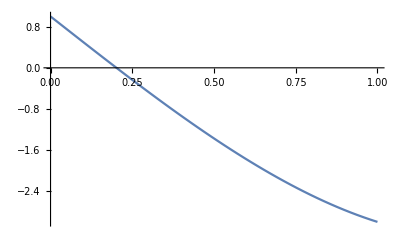

```mathematica
(* Example 1 *)
g[x_]:=x^3-5 *x+1
NewtonRaphson[0.5,5,g]
Plot[g[x],{x,0,1}]
```

k | xk | f[xk]
0 | 0.5 | -2.75
1 | 3.25 | 7.5625

Root After 5 Iteration xk = 3.25

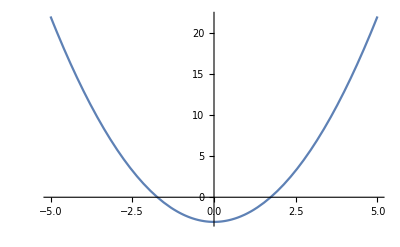

```mathematica
(* Example 2 *)
f[x_]:=x^2-3
NewtonRaphson[0.5,5,f]
Plot[f[x],{x,-5,5}]
```

k | xk | f[xk]
0 | 0.5 | 0.375
1 | 0.6666666667 | -0.03703703704

Root After 5 Iteration xk = 0.6666666667

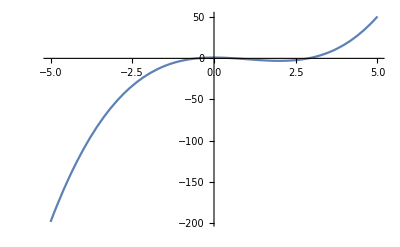

```mathematica
(* Example 3 *)
f[x_]:=x^3-3*x^2+1
NewtonRaphson[0.5,5,f]
Plot[f[x],{x,-5,5}]
```

k | xk | f[xk]
0 | 0.5 | -1.75
1 | 2.25 | 3.0625

Root After 5 Iteration xk = 2.25

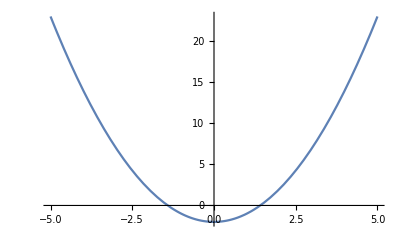

```mathematica
(* Example 4 *)
f[x_]:=x^2-2
NewtonRaphson[0.5,5,f]
Plot[f[x],{x,-5,5}]
```

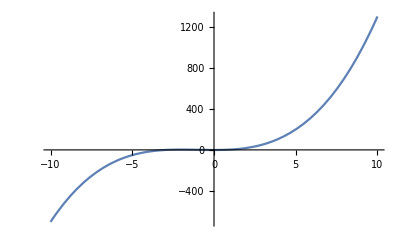

k | xk | f[xk]
0 | 1 | 3
1 | 0.6666666667 | 0.6296296296

Root After 10 Iteration xk = 0.6666666667

```mathematica
(* Example 5 *)
f[x_]:=x^3+3*(x^2)-1
Plot[f[x],{x,-10,10}]
NewtonRaphson[1,10,f]
```

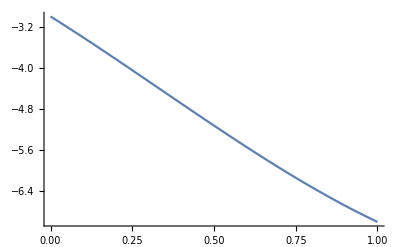

k | xk | f[xk]
0 | 0.5 | -5.125
1 | -0.7058823529 | -1.026460411

Root After 5 Iteration xk = -0.7058823529

```mathematica
(* Example 6 *)
f[x_]:=x^3-x^2-4*x-3
Plot[f[x],{x,0,1}]
NewtonRaphson[0.5,5,f]
```

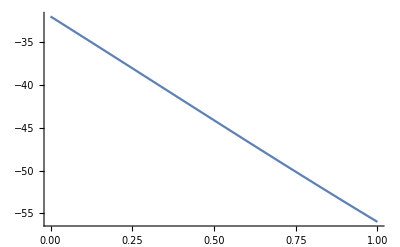

k | xk | f[xk]
0 | 0.5 | -44.125
1 | -1.319587629 | -4.369021544

Root After 5 Iteration xk = -1.319587629

```mathematica
(* Example 7 *)
f[x_]:=x^3-x^2-24*x-32
Plot[f[x],{x,0,1}]
NewtonRaphson[0.5,5,f]
```